```mathematica
<<xlr8r.m
```

xCellerator 0.88 (18-July-2012) loaded 19 July 2012 at 09:29 GMT-06:60 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 1203-002)
GNU General Public License (GPL) Terms Apply.

```mathematica
r={{A+X-> AX, Subscript[k, 1]}, {AX-> A+X, Subscript[k, 2]}, {AX -> B+X, Subscript[k, 3]}}
```

{{A+X→AX,k_1},{AX→A+X,k_2},{AX→B+X,k_3}}

```mathematica
interpret[r]
```

{{A'[t]==AX[t] k_2-A[t] k_1 X[t],AX'[t]==-AX[t] k_2-AX[t] k_3+A[t] k_1 X[t],B'[t]==AX[t] k_3,X'[t]==AX[t] k_2+AX[t] k_3-A[t] k_1 X[t]},{A,AX,B,X}}

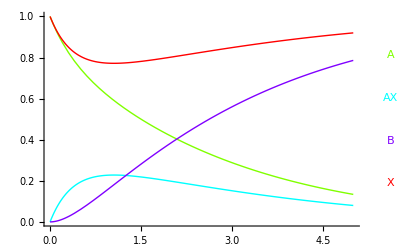

```mathematica
R={Subscript[k, 1]-> .75, Subscript[k, 2]-> .5, Subscript[k, 3]-> 1};
IC={A-> 1, X-> 1, B-> 0};
s=run[r, rates-> R, initialConditions-> IC, timeSpan-> 5];
runPlot[s]
```